## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; mu=0.3; qscal=0.54; Q=0.997;
```

```mathematica
winit=(0.25-0.00005*I)
```

0.25-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=45; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.324444+1.24077×10^-9 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
r0=rp+10^(-8);r1=45; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

0.499702

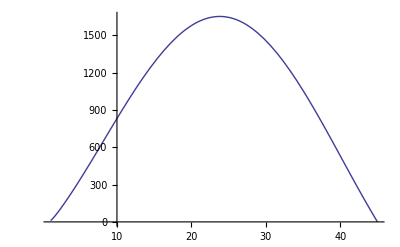

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.25+0.000005*I);
ie=0;While[ie<176,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=45+ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[radit[n],10],Re[witer[n]]},{n,0,175}];
t2r=Table[{N[radit[n],10],Im[witer[n]]},{n,0,175}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.25+0.000005*I);
ie=0;While[ie<201,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=45-ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[radit[n],10],Re[witer[n]]},{n,0,200}];
t2l=Table[{N[radit[n],10],Im[witer[n]]},{n,0,200}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{45.,1.24135×10^-9},{44.8,1.27322×10^-9},{44.6,1.30479×10^-9},{44.4,1.33947×10^-9},{44.2,1.37402×10^-9},{44.,1.40956×10^-9},{43.8,1.44622×10^-9},{43.6,1.48374×10^-9},{43.4,1.52245×10^-9},{43.2,1.56285×10^-9},{43.,1.60324×10^-9},{42.8,1.64512×10^-9},{42.6,1.68842×10^-9},{42.4,1.73348×10^-9},{42.2,1.77946×10^-9},{42.,1.82679×10^-9},{41.8,1.87554×10^-9},{41.6,1.92533×10^-9},{41.4,1.97736×10^-9},{41.2,2.03056×10^-9},{41.,2.08532×10^-9},{40.8,2.14178×10^-9},{40.6,2.19989×10^-9},{40.4,2.25975×10^-9},{40.2,2.32143×10^-9},{40.,2.38519×10^-9},{39.8,2.42515×10^-9},{39.6,2.51822×10^-9},{39.4,2.5874×10^-9},{39.2,2.65901×10^-9},{39.,2.73283×10^-9},{38.8,2.80892×10^-9},{38.6,2.88722×10^-9},{38.4,2.96819×10^-9},{38.2,3.0516×10^-9},{38.,3.13754×10^-9},{37.8,3.22616×10^-9},{37.6,3.31756×10^-9},{37.4,3.4118×10^-9},{37.2,3.50903×10^-9},{37.,3.60928×10^-9},{36.8,3.71271×10^-9},{36.6,3.78201×10^-9},{36.4,3.92951×10^-9},{36.2,4.04306×10^-9},{36.,4.16029×10^-9},{35.8,4.28123×10^-9},{35.6,4.40605×10^-9},{35.4,4.53486×10^-9},{35.2,4.66784×10^-9},{35.,4.80498×10^-9},{34.8,4.94615×10^-9},{34.6,5.09307×10^-9},{34.4,5.24413×10^-9},{34.2,5.40081×10^-9},{34.,5.56113×10^-9},{33.8,5.72656×10^-9},{33.6,5.8992×10^-9},{33.4,6.0778×10^-9},{33.2,6.25987×10^-9},{33.,6.44889×10^-9},{32.8,6.64436×10^-9},{32.6,6.84752×10^-9},{32.4,7.05555×10^-9},{32.2,7.26904×10^-9},{32.,7.49429×10^-9},{31.8,7.72449×10^-9},{31.6,7.96255×10^-9},{31.4,8.20859×10^-9},{31.2,8.46696×10^-9},{31.,8.7257×10^-9},{30.8,8.99745×10^-9},{30.6,9.2784×10^-9},{30.4,9.56876×10^-9},{30.2,9.86914×10^-9},{30.,1.01795×10^-8},{29.8,1.05004×10^-8},{29.6,1.08323×10^-8},{29.4,1.11755×10^-8},{29.2,1.15304×10^-8},{29.,1.18973×10^-8},{28.8,1.22784×10^-8},{28.6,1.26694×10^-8},{28.4,1.30757×10^-8},{28.2,1.34951×10^-8},{28.,1.39294×10^-8},{27.8,1.43806×10^-8},{27.6,1.48428×10^-8},{27.4,1.53232×10^-8},{27.2,1.58172×10^-8},{27.,1.63339×10^-8},{26.8,1.68655×10^-8},{26.6,1.74147×10^-8},{26.4,1.79836×10^-8},{26.2,1.85715×10^-8},{26.,1.91797×10^-8},{25.8,1.98084×10^-8},{25.6,2.04609×10^-8},{25.4,2.11308×10^-8},{25.2,2.18259×10^-8},{25.,2.25454×10^-8},{24.8,2.32865×10^-8},{24.6,2.40552×10^-8},{24.4,2.48473×10^-8},{24.2,2.56692×10^-8},{24.,2.65158×10^-8},{23.8,2.73924×10^-8},{23.6,2.82972×10^-8},{23.4,2.92312×10^-8},{23.2,3.0195×10^-8},{23.,3.1192×10^-8},{22.8,3.22188×10^-8},{22.6,3.32812×10^-8},{22.4,3.43759×10^-8},{22.2,3.55062×10^-8},{22.,3.66694×10^-8},{21.8,3.78694×10^-8},{21.6,3.91319×10^-8},{21.4,4.03797×10^-8},{21.2,4.1691×10^-8},{21.,4.30409×10^-8},{20.8,4.44256×10^-8},{20.6,4.58569×10^-8},{20.4,4.7324×10^-8},{20.2,4.88313×10^-8},{20.,5.03767×10^-8},{19.8,5.19627×10^-8},{19.6,5.35803×10^-8},{19.4,5.52554×10^-8},{19.2,5.6955×10^-8},{19.,5.86956×10^-8},{18.8,6.04283×10^-8},{18.6,6.23151×10^-8},{18.4,6.41315×10^-8},{18.2,6.59883×10^-8},{18.,6.79131×10^-8},{17.8,6.98534×10^-8},{17.6,7.1813×10^-8},{17.4,7.37929×10^-8},{17.2,7.57896×10^-8},{17.,7.77983×10^-8},{16.8,7.98445×10^-8},{16.6,8.18298×10^-8},{16.4,8.38402×10^-8},{16.2,8.58382×10^-8},{16.,8.78144×10^-8},{15.8,8.97599×10^-8},{15.6,9.16619×10^-8},{15.4,9.35161×10^-8},{15.2,9.53047×10^-8},{15.,9.70156×10^-8},{14.8,9.86316×10^-8},{14.6,1.00139×10^-7},{14.4,1.01517×10^-7},{14.2,1.02744×10^-7},{14.,1.03815×10^-7},{13.8,1.04652×10^-7},{13.6,1.05276×10^-7},{13.4,1.05635×10^-7},{13.2,1.05688×10^-7},{13.,1.05378×10^-7},{12.8,1.04652×10^-7},{12.6,1.03426×10^-7},{12.4,1.01592×10^-7},{12.2,9.90135×10^-8},{12.,9.54908×10^-8},{11.8,9.0764×10^-8},{11.6,8.44078×10^-8},{11.4,7.59211×10^-8},{11.2,6.44136×10^-8},{11.,4.86593×10^-8},{10.8,2.68165×10^-8},{10.6,-3.9419×10^-9},{10.4,-4.78847×10^-8},{10.2,-1.1155×10^-7},{10.,-2.04983×10^-7},{9.8,-3.43687×10^-7},{9.6,-5.51655×10^-7},{9.4,-8.66349×10^-7},{9.2,-1.3458×10^-6},{9.,-2.08101×10^-6},{8.8,-3.21385×10^-6},{8.6,-4.96649×10^-6},{8.4,-7.68603×10^-6},{8.2,-0.0000119143},{8.,-0.0000184948},{7.8,-0.0000287357},{7.6,-0.000044654},{7.4,-0.0000693358},{7.2,-0.000107458},{7.,-0.000166016},{6.8,-0.000255305},{6.6,-0.000390173},{6.4,-0.000591512},{6.2,-0.000887873},{6.,-0.001317},{5.8,-0.00192697},{5.6,-0.00277676},{5.4,-0.00393608},{5.2,-0.00548455},{5.,-0.00751073}}

```mathematica
(*The imaginary part vs the radius*)
```

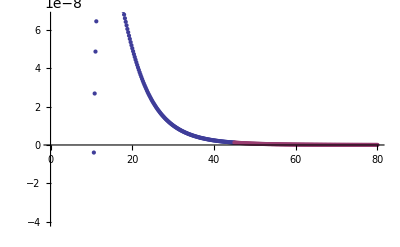

```mathematica
ListPlot[{t2l,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

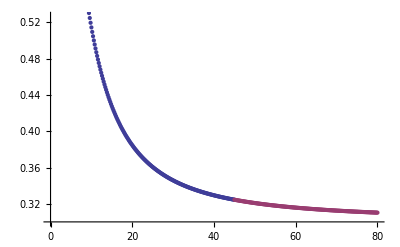

```mathematica
ListPlot[{t1l,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio1.8/Q=0.997/R.dat",Join[t1l,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio1.8/Q=0.997/I.dat",Join[t2l,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio1.8/Q=0.997/R.dat

/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio1.8/Q=0.997/I.dat

```mathematica
(*This is for estimate the "Analytical" value using Cardoso's bomb *)
```

```mathematica
(*Radius*)
```

```mathematica
rp=M+Sqrt[M^2-Q^2]
rm=M-Sqrt[M^2-Q^2]
rmirror=40
```

1.6

0.4

40

```mathematica
(*Frequencies*)
```

```mathematica
wc=qscal*Q/rp
wtilde=(wa-wc)*(rp^2/(rp-rm))
```

0.45

2.13333 (-0.45+wa)

```mathematica
(*Nodes*)
```

```mathematica
n=0
```

0

```mathematica
(*First aproximation, the root of the Bessel function (has to be the n+1 root, otherwise the 1st is zero!)*)
```

```mathematica
jl12n=N[BesselJZero[l+1/2,n+1],10]
```

4.493409459

```mathematica
wfa=jl12n/rmirror
```

0.1123352365

```mathematica
(*Let's calculate the imaginary part, delta, we need some definitions in advance*)
```

```mathematica
Product[i^2+4*wtilde^2,{i,1,l}]
```

1+18.2044 (-0.45+wa)^2

```mathematica
gamm=(Factorial[l]/Factorial2[(2*l-1)])^2*rp^2*(rp-rm)^(2*l)/Factorial[2*l]/Factorial[2*l+1]*2/(2*l+1)*Product[i^2+4*wtilde^2,{i,1,l}]*jl12n^(2*l+1)
```

18.5805 (1+18.2044 (-0.45+wa)^2)

```mathematica
Dbess=D[BesselJ[l+1/2,x],x]/.x->jl12n
```

-0.367413504

```mathematica
f1=(-1)^(l)*BesselJ[-l-1/2,jl12n]/Dbess
```

1.049528

```mathematica
f2=(wfa-wc)/rmirror^(2*l+2)
```

-1.319×10^-7

```mathematica
(*Imaginary part delta*)
```

```mathematica
deltat=-gamm*f1*f2/.wa->wfa
```

7.91099×10^-6

```mathematica
(*make a list of the 1/r decay*)
```

```mathematica
tan=Table[jl12n/i,{i,50}];
```

```mathematica
(*Compare the behaviour of Re[w] in a plot*)
```



```mathematica
ListPlot[{t1l,t1r,tan}]
```